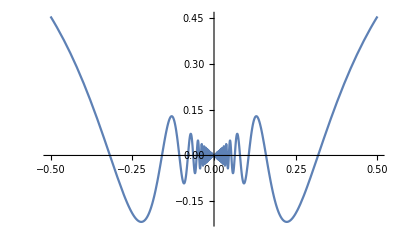

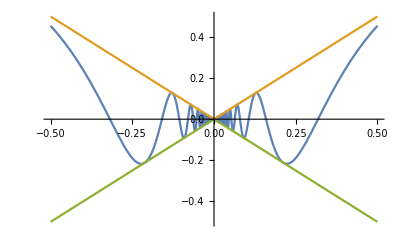

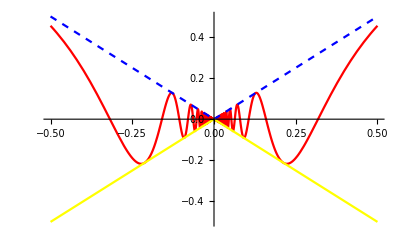

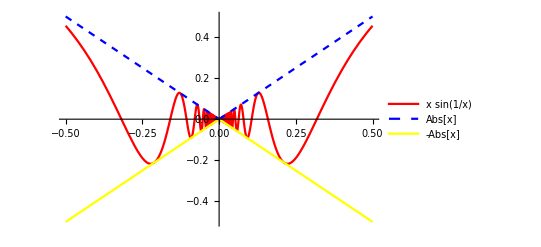

-Graphics-

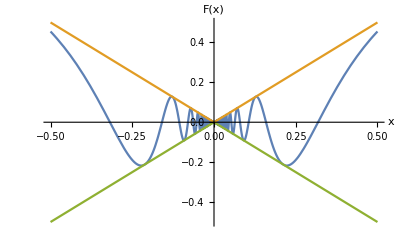

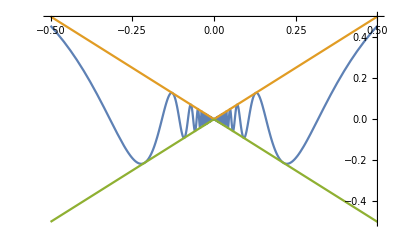

-Graphics-

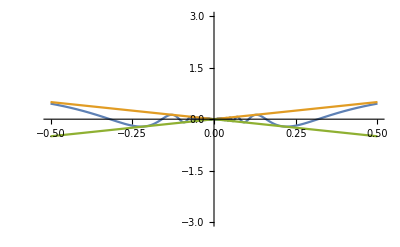

-Graphics-

-Graphics-

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

1/((-1/2+ⅇ^(ⅈ w))^2)

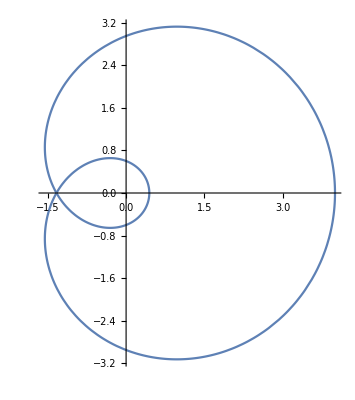

-Graphics3D-

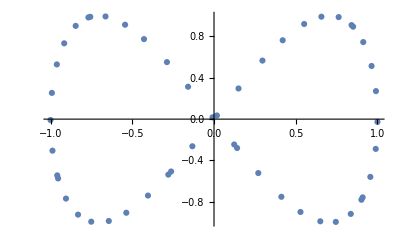

-Graphics3D-

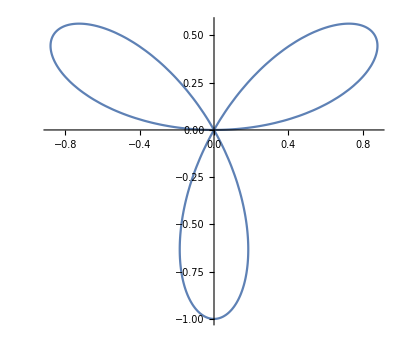

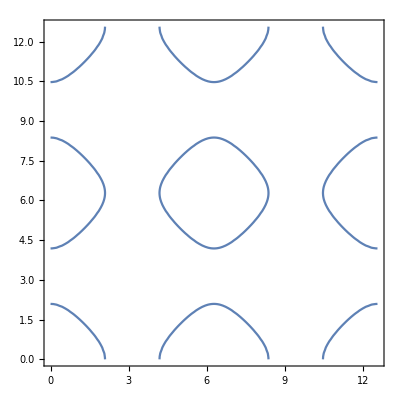

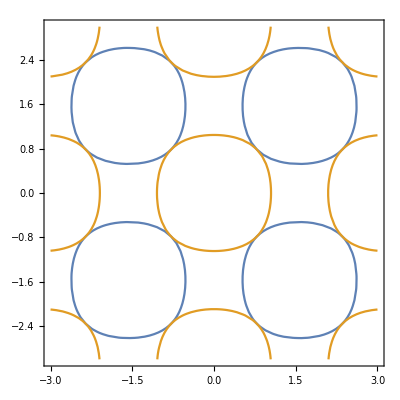

```mathematica
Plot[x*Sin[1/x], {x,-1/2, 1/2}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, PlotStyle->{ Red, Directive[Dashed, Blue], Yellow}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, PlotStyle->{ Red, Directive[Dashed, Blue], Yellow}, PlotLegends->"Expressions"]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, Axes -> {True,False}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, AxesLabel-> {x,F[x]}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, AxesOrigin->{.5,.5}]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, PlotRange-> Full]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, PlotRange-> 3]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, ColorFunction-> Function[{x,y}, Hue[x]]]
Plot[{x*Sin[1/x],Abs[x], -Abs[x]}, {x,-1/2, 1/2}, ColorFunction-> Function[{x,y}, Hue[y]]]
Plot3D[Sin[x+y^2], {x,-3,3},{y,-2,2}]
Plot3D[Sin[x+y^2], {x,-3,3},{y,-2,2} , ColorFunction-> Function[{x,y,z}, Hue[z]]]
Plot3D[Sin[x+y^2], {x,-3,3},{y,-2,2}, Mesh-> None]
Plot3D[Sin[x+y^2], {x,-3,3},{y,-2,2}, Mesh-> 4, MeshStyle-> Blue]
Clear["Global`*"]
Remove["Global`*"]
h = 1/(s-1/2)^2 /. s -> Exp[I w]
ParametricPlot[{Re[h],Im[h]}, {w,0,2*Pi}]
ParametricPlot3D[{Sin[x], Cos[x], x/10}, {x,0,20}]
Manipulate[Plot[a*x^2+ b*x + c, {x,-10,10}], {a, -10,10}, {b,-10,10}, {c,-10,10}]
Manipulate[Factor[n^n+1], {n, 10,100,13}]
ListPlot[Table[{Sin[x], Sin[2 x]}, {x,50}]]
SphericalPlot3D[{1,2,3}, {θ,0,Pi/2}, {Φ, 0, 3*Pi/2}]
PolarPlot[Sin[3*t], {t,0,Pi}]
ContourPlot[Cos[x]+ Cos[y] == 1/2, {x,0,4*Pi}, {y,0,4*Pi}]
ContourPlot[{Abs[Sin[x]* Sin[y]]== .5 , Abs[Cos[x]*Cos[y]] == .5}, {x,-3,3},{y,-3,3}]
```